```mathematica
Quit[]
```

## Set Notebook Directory.

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Krzysztof\Desktop\Magisterka\Praca-magisterska\Code\Maxim-axion

## Initialise all necessary lists.

```mathematica
qValuesList = {} (*comoving momentum list*);
maValuesList={} (*Initialize list: mass of axion, [eV]*);
faValuesList = {} (*Initialize list: scale of spontaneous breaking of the PQ symmetry, [GeV]*);
AparameterList = {} (*Initialize list: one of the parameter, which we need to fit*);
bparameterList = {} (*Initialize list: one of the parameter, which we need to fit*);
μparameterList = {} (*Initialize list: one of the parameter which, we need to fit*);
```

## Read data from file.

We have two file, which contain all the necessary information that we need: `q.csv` - contains values of the q=p/T, comoving momentum of our interest. The range of comoving momentum of our interest is in range [0, 20]. The second file contains the value of the: `f(q) * q^2`, where `f(q)` is function distribution of axion particles. We have those function distribution for specific values od the parameter `f_a` of that axions. That range, which has been mentioned is f_a = [1, 100]*10^7 GeV.

```mathematica
(********** Step 1:Import the CSV file, `q.csv`**********)
data=Import["q.csv","CSV"];
qValuesList = data[[1]];

(********** Step 2:Import the CSV file, `Distributions.csv` **********)
data=Import["Distributions.csv","CSV"];
(*** fa list ***)
faValuesList=data[[2;;,1]]; (*Skip the header row and extract the first element from each subsequent row: there will be fa value*)

(*** distribution list ***)
(*Separate header and data*)
header=data[[1]];                 (*Extract the header row*)
dataWithoutHeader=data[[2;;]];   (*Extract the data without the header row*)

(*Skip the first element in each data row*)
distributionsQPow2=Rest/@dataWithoutHeader; (*Output the processed data without header, `f(q) * q^2*)
(*Here we have to divide each elelemt by q^2, `f(q)`*)
distributions = Map[MapThread[Times,{#,qValuesList^-2}]&,distributionsQPow2];
(* f(q) * q^3*)
distributionsQPow3 = Map[MapThread[Times,{#,qValuesList}]&,distributionsQPow2];
(********** Step 3: find mass list **********)
maValuesList=If[Length[faValuesList]!=0,5.69151*10^6/faValuesList,{}];

(********** Step 4: sety some constants **********)
NumberOfDistributions = Length[faValuesList];

(********** Step 5: Check List, sanity checks **********)
(*Print["qValuesList", qValuesList, "len(qValuesList)=", Length[qValuesList]];
Print["faValuesList", faValuesList, "len(faValuesList)=", Length[faValuesList]];
Print["maValuesList", maValuesList, "len(maValuesList)=", Length[maValuesList]];*)
(*Print["len(distributionsQPow3)",Length[distributionsQPow3]]*)
Print["qValuesList", qValuesList, "len(qValuesList)=", Length[qValuesList]]
Print["maValuesList", maValuesList, "len(maValuesList)=", Length[maValuesList]]
Print["faValuesList", faValuesList, "len(faValuesList)=", Length[faValuesList]]

(*Print["distributionsQPow3", distributionsQPow3, "len(distributionsQPow3)", distributionsQPow3]*)
```

qValuesList{0.0001,0.100602,0.201104,0.301606,0.402108,0.50261,0.603112,0.703614,0.804116,0.904618,1.00512,1.10562,1.20612,1.30663,1.40713,1.50763,1.60813,1.70863,1.80914,1.90964,2.01014,2.11064,2.21114,2.31165,2.41215,2.51265,2.61315,2.71365,2.81416,2.91466,3.01516,3.11566,3.21616,3.31667,3.41717,3.51767,3.61817,3.71867,3.81918,3.91968,4.02018,4.12068,4.22118,4.32169,4.42219,4.52269,4.62319,4.72369,4.8242,4.9247,5.0252,5.1257,5.2262,5.32671,5.42721,5.52771,5.62821,5.72871,5.82922,5.92972,6.03022,6.13072,6.23122,6.33173,6.43223,6.53273,6.63323,6.73373,6.83424,6.93474,7.03524,7.13574,7.23624,7.33675,7.43725,7.53775,7.63825,7.73875,7.83926,7.93976,8.04026,8.14076,8.24126,8.34177,8.44227,8.54277,8.64327,8.74377,8.84428,8.94478,9.04528,9.14578,9.24628,9.34679,9.44729,9.54779,9.64829,9.74879,9.8493,9.9498,10.0503,10.1508,10.2513,10.3518,10.4523,10.5528,10.6533,10.7538,10.8543,10.9548,11.0553,11.1558,11.2563,11.3568,11.4573,11.5578,11.6583,11.7588,11.8593,11.9598,12.0603,12.1608,12.2613,12.3618,12.4623,12.5629,12.6634,12.7639,12.8644,12.9649,13.0654,13.1659,13.2664,13.3669,13.4674,13.5679,13.6684,13.7689,13.8694,13.9699,14.0704,14.1709,14.2714,14.3719,14.4724,14.5729,14.6734,14.7739,14.8744,14.9749,15.0754,15.1759,15.2764,15.3769,15.4774,15.5779,15.6784,15.7789,15.8794,15.9799,16.0804,16.1809,16.2814,16.3819,16.4824,16.5829,16.6834,16.7839,16.8844,16.9849,17.0854,17.1859,17.2864,17.3869,17.4874,17.588,17.6885,17.789,17.8895,17.99,18.0905,18.191,18.2915,18.392,18.4925,18.593,18.6935,18.794,18.8945,18.995,19.0955,19.196,19.2965,19.397,19.4975,19.598,19.6985,19.799,19.8995,20}len(qValuesList)=200

maValuesList{0.569151,0.379434,0.284576,0.22766,0.189717,0.162615,0.142288,0.126478,0.11383,0.103482,0.0948585,0.0875617,0.0813073,0.0758868,0.0711439,0.0669589,0.063239,0.0599106,0.0569151,0.0542049,0.051741,0.0494914,0.0474293,0.0455321,0.0437808,0.0421593,0.0406536,0.0392518,0.0379434,0.0367194,0.0355719,0.034494,0.0334795,0.0325229,0.0316195,0.0307649,0.0299553,0.0291872,0.0284576,0.0277635,0.0271024,0.0264721,0.0258705,0.0252956,0.0247457,0.0242192,0.0237146,0.0232307,0.022766,0.0223196,0.0218904,0.0214774,0.0210797,0.0206964,0.0203268,0.0199702,0.0196259,0.0192933,0.0189717,0.0186607,0.0183597,0.0180683,0.017786,0.0175123,0.017247,0.0169896,0.0167397,0.0164971,0.0162615,0.0160324,0.0158098,0.0155932,0.0153825,0.0151774,0.0149777,0.0147831,0.0145936,0.0144089,0.0142288,0.0140531,0.0138817,0.0137145,0.0135512,0.0133918,0.0132361,0.0130839,0.0129352,0.0127899,0.0126478,0.0125088,0.0123728,0.0122398,0.0121096,0.0119821,0.0118573,0.0117351,0.0116153,0.011498,0.011383,0.0112703,0.0111598,0.0110515,0.0109452,0.010841,0.0107387,0.0106383,0.0105398,0.0104431,0.0103482,0.010255,0.0101634,0.0100735,0.00998511,0.00989828,0.00981295,0.00972908,0.00964663,0.00956556,0.00948585,0.00940745,0.00933034,0.00925449,0.00917985,0.00910642,0.00903414,0.00896301,0.00889298,0.00882405,0.00875617,0.00868933,0.0086235,0.00855866,0.00849479,0.00843187,0.00836987,0.00830877,0.00824857,0.00818922,0.00813073,0.00807306,0.00801621,0.00796015,0.00790488,0.00785036,0.00779659,0.00774355,0.00769123,0.00763961,0.00758868,0.00753842,0.00748883,0.00743988,0.00739157,0.00734388,0.00729681,0.00725033,0.00720444,0.00715913,0.00711439,0.0070702,0.00702656,0.00698345,0.00694087,0.0068988,0.00685724,0.00681618,0.00677561,0.00673551,0.00669589,0.00665674,0.00661803,0.00657978,0.00654197,0.00650458,0.00646762,0.00643108,0.00639496,0.00635923,0.0063239,0.00628896,0.00625441,0.00622023,0.00618642,0.00615298,0.0061199,0.00608718,0.0060548,0.00602276,0.00599106,0.0059597,0.00592866,0.00589794,0.00586754,0.00583745,0.00580766,0.00577818,0.005749,0.00572011,0.00569151}len(maValuesList)=199

faValuesList{10000000,15000000,20000000,25000000,30000000,35000000,40000000,45000000,50000000,55000000,60000000,65000000,70000000,75000000,80000000,85000000,90000000,95000000,100000000,105000000,110000000,115000000,120000000,125000000,130000000,135000000,140000000,145000000,150000000,155000000,160000000,165000000,170000000,175000000,180000000,185000000,190000000,195000000,200000000,205000000,210000000,215000000,220000000,225000000,230000000,235000000,240000000,245000000,250000000,255000000,260000000,265000000,270000000,275000000,280000000,285000000,290000000,295000000,300000000,305000000,310000000,315000000,320000000,325000000,330000000,335000000,340000000,345000000,350000000,355000000,360000000,365000000,370000000,375000000,380000000,385000000,390000000,395000000,400000000,405000000,410000000,415000000,420000000,425000000,430000000,435000000,440000000,445000000,450000000,455000000,460000000,465000000,470000000,475000000,480000000,485000000,490000000,495000000,500000000,505000000,510000000,515000000,520000000,525000000,530000000,535000000,540000000,545000000,550000000,555000000,560000000,565000000,570000000,575000000,580000000,585000000,590000000,595000000,600000000,605000000,610000000,615000000,620000000,625000000,630000000,635000000,640000000,645000000,650000000,655000000,660000000,665000000,670000000,675000000,680000000,685000000,690000000,695000000,700000000,705000000,710000000,715000000,720000000,725000000,730000000,735000000,740000000,745000000,750000000,755000000,760000000,765000000,770000000,775000000,780000000,785000000,790000000,795000000,800000000,805000000,810000000,815000000,820000000,825000000,830000000,835000000,840000000,845000000,850000000,855000000,860000000,865000000,870000000,875000000,880000000,885000000,890000000,895000000,900000000,905000000,910000000,915000000,920000000,925000000,930000000,935000000,940000000,945000000,950000000,955000000,960000000,965000000,970000000,975000000,980000000,985000000,990000000,995000000,1000000000}len(faValuesList)=199

## Collect data into groups and set approx distribution function.

Here we try to transpose data in such a way to have a value of the comoving momenta and proper value of the function distribution (maybe multiply with some power of comoving momenta) - the less operation with data, the better results I will get. Important in the third line you set how look the `axion distribution function` in shortcut: `AxDistFunction`. In generall I suggest to use: `f(q)*q^3`.

```mathematica
(*Helpfull function to create Transposed data, remeber that `i` will refer to vale of `f_a` in `faList`.*)
transposeData[i_,list_,listOfLists_List]:=Transpose[{list,listOfLists[[i]]}]
(*Transpose data numerous of times*)
AxDistFunctionTabList=Table[transposeData[i,qValuesList,distributionsQPow3],{i,NumberOfDistributions}]; (* f(q)*q^3 *)
AxDistFunctionList=Table[Interpolation[AxDistFunctionTabList[[i]],Method->"Spline",InterpolationOrder->3],{i,NumberOfDistributions}];
(*Defined the approx axion distribution function, `f(q)*q^3`*)
(*fApprox[x_,A_,b_,μ_]:=x^3*A(1/(Exp[x/b + μ]-1))*)
(*fApprox[x_,A_,b_,μ_]:=x^2 √(1+x^2)*(Exp[A(√(1+x^2)-b)+μ])^-1*)
(*fApprox[x_,A_,b_,μ_]:=x^2(Exp[A(√(1+x^2)-b)+μ])^-1*)
(*fApprox[x_,A_,b_]:=x^2(Exp[A(√(1+x^2)-b)])^-1*)
(*fApprox[x_,A_,b_]:=x^2(Exp[A √(1+x^2)-b])^-1*)
fApprox[x_,A_,b_,μ_]:=x^2(Exp[A √(1+x^2)-b]+μ)^-1
```

## (Optional) sanity check of interpolation.

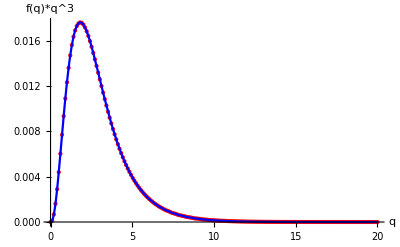

```mathematica
(*Plot original data points and the interpolated function on the same plot*)Show[ListPlot[AxDistFunctionTabList[[199]],PlotStyle->{Red,PointSize[Large]},AxesLabel->{"q","f(q)*q^3"}],Plot[AxDistFunctionList[[199]][x],{x,Min[qValuesList],Max[qValuesList]},PlotStyle->Blue]]
```

## (Optional) select a distribution and make a fit - update way of finding fit.

best fit parameters: {A→0.748901,b→-0.0988714,μ→0.370751}[]

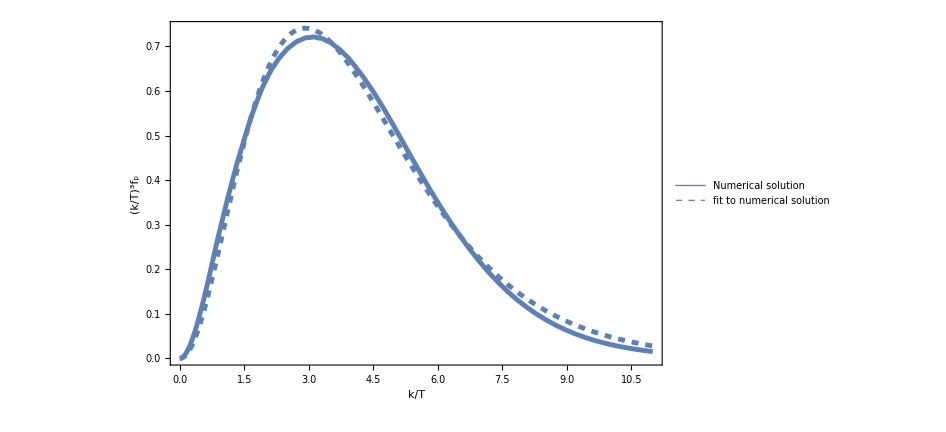

```mathematica
(********** Step 1: Settings to make a fit **********)
SelectedDist = AxDistFunctionList[[1]];
xmin = 0.0;
xmax = 11;
step = 0.005;
dataToFit=Table[{x,SelectedDist[x]},{x,xmin,xmax,step}];
(********** Step 2: Perform the nonlinear fit **********)
fit=NonlinearModelFit[dataToFit,{fApprox[x,A,b,μ]},{A,b,μ},x,
Method->{"NMinimize",Method->{"RandomSearch","SearchPoints"->100}}];
(*fit=NonlinearModelFit[dataToFit,{fApprox[x,A,b]},{A,b},x,
Method->{"NMinimize",Method->{"RandomSearch","SearchPoints"->100}}];*)
(********** Step 3: Optional information **********)
(*Extract best-fit parameters*)
bestFitParams=fit["BestFitParameters"];
Print["best fit parameters:"bestFitParams[]];
(*Visualize the fit*)
(*Show[ListPlot[data],Plot[fit[x],{x,xmin,xmax},PlotStyle->Red]]*)

(********** Step 4: Plot distribution and fit **********)
Plot[{SelectedDist[x], fit[x]},{x,0,11},Frame->True,FrameLabel->{{"(k/T)^3f_p",None},{"k/T",None}},LabelStyle->22,FrameStyle->Directive[Black,Thick],PlotStyle->{{Thickness[0.005],ColorData[97,1]},{Dashed,Thickness[0.005],ColorData[97,1]},{Thickness[0.005],Orange,ColorData[97,2]}},

PlotLegends->{"Numerical solution","fit to numerical solution"},
ImageSize-> 700]
```

## Find all parameters for each distribution function.

We already create two list: `maValuesList` - axion masses and `faValuesList` -  scale of spontaneous breaking of the PQ symmetry. Now we have to read the distribution function and find parameters, which describes best fit to data stored in `AxDistFunctionTabList`. We need this because in the end we are looking for function: A(m_a), b(m_a) and μ(m_a), where A, b and μ are parameters which we will find out.

```mathematica
(*clear up*)
AparameterList = {};
bparameterList = {};
μparameterList = {};

(*find parameters*)
For[i=1,i<=NumberOfDistributions,i++,
If[Mod[i,10]==0,Print["step: ",i]];
(********** Step 1: Settings to make a fit **********)
SelectedDist = AxDistFunctionList[[i]];
xmin = 0.0;
xmax = 11;
step = 0.005;
dataToFit=Table[{x,SelectedDist[x]},{x,xmin,xmax,step}];
(********** Step 2: Perform the nonlinear fit **********)
fit=NonlinearModelFit[dataToFit,{fApprox[x,A,b,μ]},{A,b,μ},x,
Method->{"NMinimize",Method->{"RandomSearch","SearchPoints"->100}}];
(*fit=NonlinearModelFit[dataToFit,{fApprox[x,A,b]},{A,b},x,
Method->{"NMinimize",Method->{"RandomSearch","SearchPoints"->100}}];*)

(********** Step 3: Find the best parameters and Append them to right List **********)
bestFitParams={A,b,μ}/.fit["BestFitParameters"];
(*bestFitParams={A,b}/.fit["BestFitParameters"];*)
AppendTo[AparameterList,bestFitParams[[1]] ];
AppendTo[bparameterList,bestFitParams[[2]] ];
AppendTo[μparameterList,bestFitParams[[3]] ];
]
(***Test my results***)
(*Print["AparameterList", AparameterList, "len(AparameterList)", Length[AparameterList]];
Print["bparameterList", bparameterList, "len(bparameterList)", Length[bparameterList]];*)
(*Print["μparameterList", μparameterList, "len(μparameterList)", Length[μparameterList]];*)
```

step: 10

step: 20

step: 30

step: 40

step: 50

step: 60

step: 70

step: 80

step: 90

step: 100

step: 110

step: 120

step: 130

step: 140

step: 150

step: 160

step: 170

step: 180

step: 190

## Find function A(m_a), b(m_a) and μ(m_a).

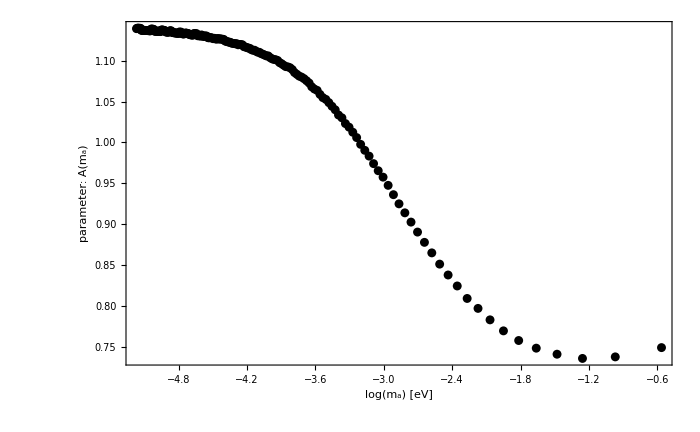

```mathematica
(********************************************* deal with parameter A ****************************************************)
dataParameterA = Transpose[{Log[maValuesList],AparameterList}]; (*Combine maValuesList and AparameterList into a list of data points*)
(******** to proper work with plot ********)
xmin = Min[Log[maValuesList]];
ymin = Min[AparameterList];
xmax = Max[Log[maValuesList]];
ymax = Max[AparameterList];

(********Plot the data with black dots********)
Show[ListPlot[dataParameterA,PlotStyle->Black, PlotRange->{{xmin,xmax},{ymin,ymax}}, Frame->True,FrameLabel->{{"parameter: A(m_a)",None},{"log(m_a) [eV]",None}}, LabelStyle->22,FrameStyle->Directive[Black,Thick], ImageSize-> 700]
]
```

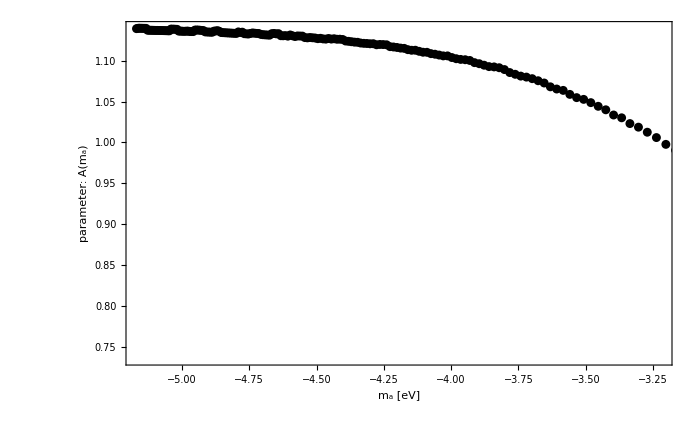

```mathematica
(******** to proper work with plot ********)
xmin = Min[Log[maValuesList]];
ymin = Min[AparameterList];
xmax =Log[0.1*2/5];
ymax = Max[AparameterList];

(******** Plot the data with black dots ********)
Show[ListPlot[dataParameterA,PlotStyle->Black, PlotRange->{{xmin,xmax},{ymin,ymax}}, Frame->True,FrameLabel->{{"parameter: A(m_a)",None},{"m_a [eV]",None}}, LabelStyle->22,FrameStyle->Directive[Black,Thick], ImageSize-> 700]
]
```

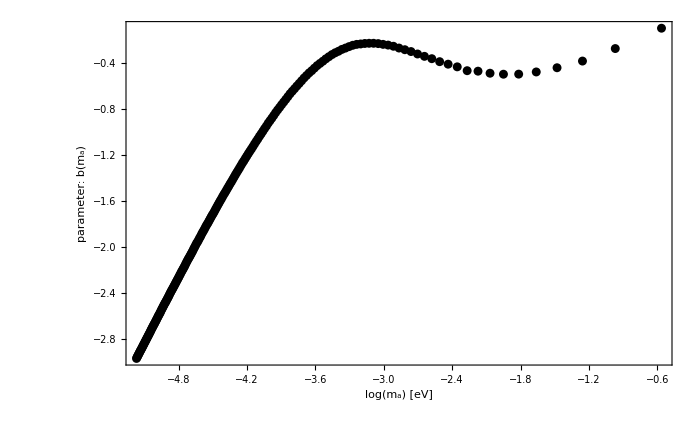

```mathematica
(********************************************* deal with parameter b ****************************************************)
dataParameterb = Transpose[{Log[maValuesList],bparameterList}]; (*Combine maValuesList and AparameterList into a list of data points*)
(******** to proper work with plot ********)
xmin = Min[Log[maValuesList]];
ymin = Min[bparameterList];
xmax =Max[Log[maValuesList]];
ymax = Max[bparameterList];
(******** Plot the data with black dots ********)
Show[ListPlot[dataParameterb,PlotStyle->Black, PlotRange->{{xmin,xmax},{ymin,ymax}}, Frame->True,FrameLabel->{{"parameter: b(m_a)",None},{"log(m_a) [eV]",None}}, LabelStyle->22,FrameStyle->Directive[Black,Thick], ImageSize-> 700]
]
```

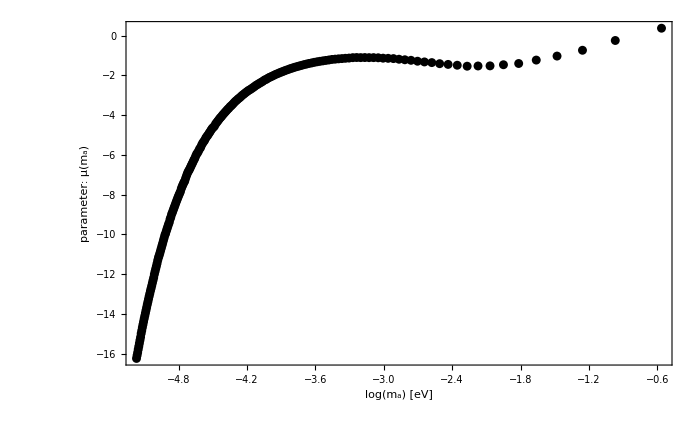

```mathematica
(********************************************* deal with parameter μ ****************************************************)
dataParameterμ = Transpose[{Log[maValuesList],μparameterList}]; (*Combine maValuesList and AparameterList into a list of data points*)
(********to proper work with plot********)
xmin = Min[Log[maValuesList]];
ymin = Min[μparameterList];
xmax =Max[Log[maValuesList]];
ymax = Max[μparameterList];

(******** Plot the data with black dots ********)
Show[ListPlot[dataParameterμ,PlotStyle->Black, PlotRange->{{xmin,xmax},{ymin,ymax}}, Frame->True,FrameLabel->{{"parameter: μ(m_a)",None},{"log(m_a) [eV]",None}}, LabelStyle->22,FrameStyle->Directive[Black,Thick], ImageSize-> 700]
]
```

## Find fit funtion: A(m_a), b(m_a) and μ(m_a)

FittedModel[2.21021+8.96381 x+23.5513 x^2+35.2546 x^3+33.5196 x^4+21.3951 x^5+9.436 x^6+2.906 x^7+0.622193 x^8+0.0906448 x^9+0.00856223 x^10+0.000472657 x^11+0.0000115747 x^12]

2.21021+8.96381 x+23.5513 x^2+35.2546 x^3+33.5196 x^4+21.3951 x^5+9.436 x^6+2.906 x^7+0.622193 x^8+0.0906448 x^9+0.00856223 x^10+0.000472657 x^11+0.0000115747 x^12

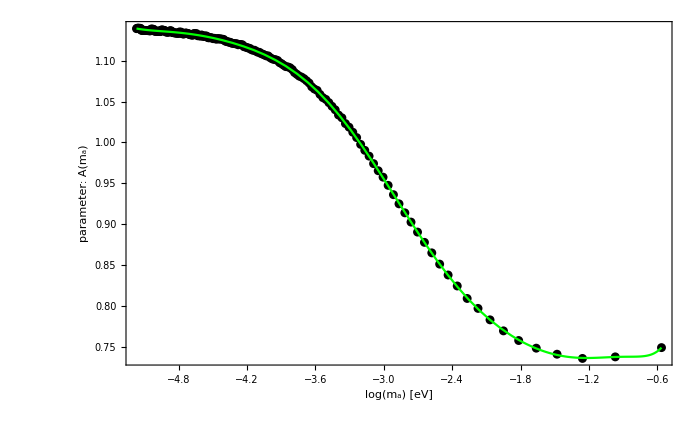

```mathematica
(********************************************* deal with parameter A ****************************************************)
(*Combine maValuesList and AparameterList into a list of points*)
dataParameterA = Transpose[{Log[maValuesList],AparameterList}]; 
(*Use FindFormula to find a suitable model for the data*)
polyModA=LinearModelFit[dataParameterA,Table[x^i,{i,1,12}],x]
polyModA["BestFit"]

(******** to proper work with plot ********)
xmin = Min[Log[maValuesList]];
ymin = Min[AparameterList];
xmax = Max[Log[maValuesList]];
ymax = Max[AparameterList];
input=Log[maValuesList];
(******** plotting ********)
Show[ListPlot[dataParameterA,PlotStyle->Black, PlotRange->{{xmin,xmax},{ymin,ymax}}, Frame->True,FrameLabel->{{"parameter: A(m_a)",None},{"log(m_a) [eV]",None}}, LabelStyle->22,FrameStyle->Directive[Black,Thick], ImageSize-> 700],
Plot[polyModA[x],{x,Min@input,Max@input},PlotStyle->Green]
]
```

FittedModel[3.29467+21.0035 x+57.2703 x^2+89.892 x^3+88.4219 x^4+57.3174 x^5+25.0581 x^6+7.40558 x^7+1.45427 x^8+0.181453 x^9+0.013006 x^10+0.000407576 x^11]

3.29467+21.0035 x+57.2703 x^2+89.892 x^3+88.4219 x^4+57.3174 x^5+25.0581 x^6+7.40558 x^7+1.45427 x^8+0.181453 x^9+0.013006 x^10+0.000407576 x^11

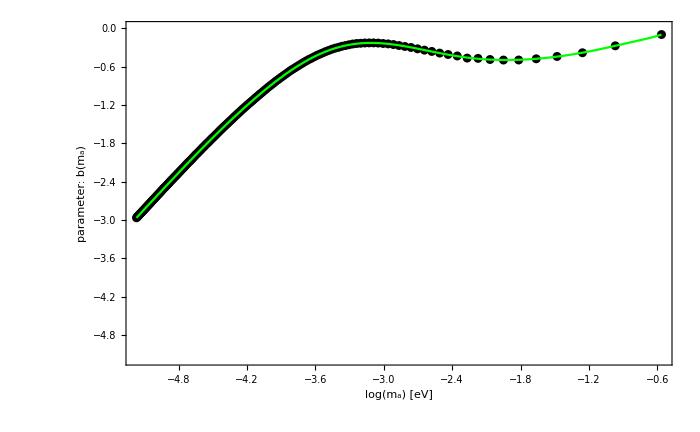

```mathematica
(********************************************* deal with parameter b ****************************************************)
(*Combine maValuesList and AparameterList into a list of points*)
dataParameterb = Transpose[{Log[maValuesList],bparameterList}]; 
(*Use FindFormula to find a suitable model for the data*)
polyModb=LinearModelFit[dataParameterb,Table[x^i,{i,1,11}],x]
polyModb["BestFit"]

(******** to proper work with plot ********)
xmin = Min[Log[maValuesList]];
ymin = Min[dataParameterb];
xmax = Max[Log[maValuesList]];
ymax = 0;
input=Log[maValuesList];
(******** plotting ********)
Show[ListPlot[dataParameterb,PlotStyle->Black, PlotRange->{{xmin,xmax},{ymin,ymax}}, Frame->True,FrameLabel->{{"parameter: b(m_a)",None},{"log(m_a) [eV]",None}}, LabelStyle->22,FrameStyle->Directive[Black,Thick], ImageSize-> 700],
Plot[polyModb[x],{x,Min@input,Max@input},PlotStyle->Green]
]
```

FittedModel[-77.3199-481.492 x-1266.56 x^2-1891.93 x^3-1807.42 x^4-1171.03 x^5-530.747 x^6-170.473 x^7-38.6927 x^8-6.07531 x^9-0.628251 x^10-0.0385072 x^11-0.00105989 x^12]

-77.3199-481.492 x-1266.56 x^2-1891.93 x^3-1807.42 x^4-1171.03 x^5-530.747 x^6-170.473 x^7-38.6927 x^8-6.07531 x^9-0.628251 x^10-0.0385072 x^11-0.00105989 x^12

0.370751

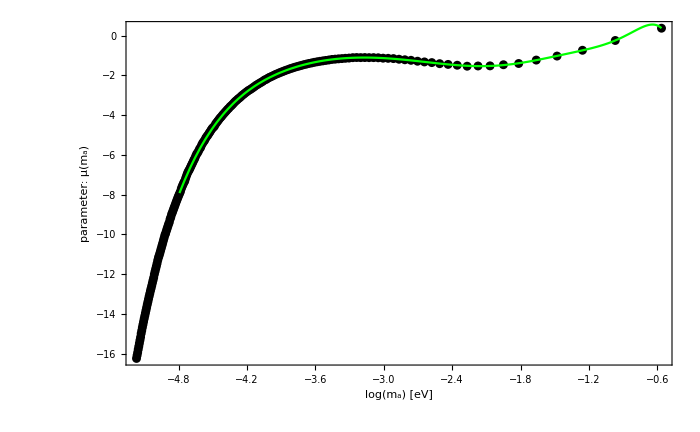

```mathematica
(********************************************* deal with parameter μ ****************************************************)
(*Combine maValuesList and AparameterList into a list of points*)
dataParameterμ = Transpose[{Log[maValuesList],μparameterList}]; 
(*Use FindFormula to find a suitable model for the data*)
polyModμ=LinearModelFit[dataParameterμ,Table[x^i,{i,1,12}],x]
polyModμ["BestFit"]

(******** to proper work with plot ********)
xmin = Min[Log[maValuesList]];
ymin = Min[dataParameterμ];
xmax = Max[Log[maValuesList]];
ymax = Max[dataParameterμ]
input=Log[maValuesList];
(******** plotting ********)
Show[ListPlot[dataParameterμ,PlotStyle->Black, PlotRange->{{xmin,xmax},{ymin,ymax}}, Frame->True,FrameLabel->{{"parameter: μ(m_a)",None},{"log(m_a) [eV]",None}}, LabelStyle->22,FrameStyle->Directive[Black,Thick], ImageSize-> 700],
Plot[polyModμ[x],{x,Min@input,Max@input},PlotStyle->Green]
]
```

## Second interpolation

{{Null},{Null}}

A = Int of q^3 f(q) (MAXIM): 3.64511

B = Int of x^2(Exp[A√(1 + SuperscriptBox[x, 2])-b]+μ)^-1: 3.68766

|A-B| / A = 1.16741 %

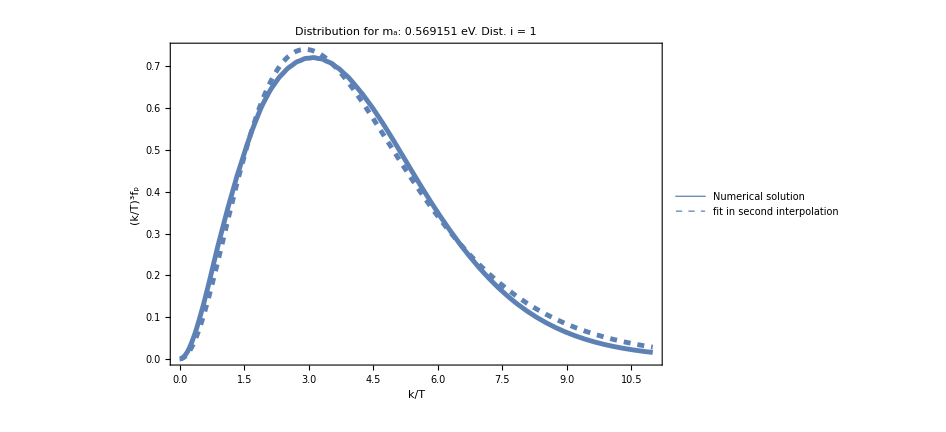

```mathematica
(********** Select distribution that we already have **********)
NumberOfDist = 1;
SelectedDist = AxDistFunctionList[[NumberOfDist]];
SelectedMass = maValuesList[[NumberOfDist]];
(********** Numerical Solution in second interpolation **********)
Avalue = polyModA[Log[SelectedMass]];
{{bvalue = polyModb[Log[SelectedMass]];}, {μvalue = polyModμ[Log[SelectedMass]];}}

(********** Compute the integral of the selected distributions **********)
upperLimit=13;
Print["A = Int of q^3 f(q) (MAXIM): ",integralF=NIntegrate[SelectedDist[x],{x,0,upperLimit}]]
Print["B = Int of x^2(Exp[A√(1 + SuperscriptBox[x, 2])-b]+μ)^-1: ",integralFit = NIntegrate[fApprox[x,Avalue,bvalue,μvalue],{x,0,upperLimit}]]
Print["|A-B| / A = ", Abs[integralF -integralFit]/ integralF *100, " %"]
(********** Plot distribution and fit **********)
Plot[{SelectedDist[x], fApprox[x,Avalue,bvalue,μvalue]},{x,0,11},Frame->True,FrameLabel->{{"(k/T)^3f_p",None},{"k/T",None}},LabelStyle->22,FrameStyle->Directive[Black,Thick],PlotStyle->{{Thickness[0.005],ColorData[97,1]},{Dashed,Thickness[0.005],ColorData[97,1]},{Thickness[0.005],Orange,ColorData[97,2]}},

PlotLegends->{"Numerical solution","fit in second interpolation"},
PlotLabel->"Distribution for m_a: "  <> ToString[SelectedMass] <> " eV. Dist. i = " <> ToString [NumberOfDist],
ImageSize-> 700]
```

## Comparison to Bose-Einstein and Boltzmann distribution

f_a: 10000000 GeV

{{Null},{Null}}

3.64511

NIntegrate::inumr: The integrand C ⅇ^-x x^3 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,13}}.

{C→0.608157}

NIntegrate::inumr: The integrand (C x^3)/(-1+ⅇ^x) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,13}}.

{C→0.561855}

{C→0.608157}

{C→0.561855}

3.64511

3.64511

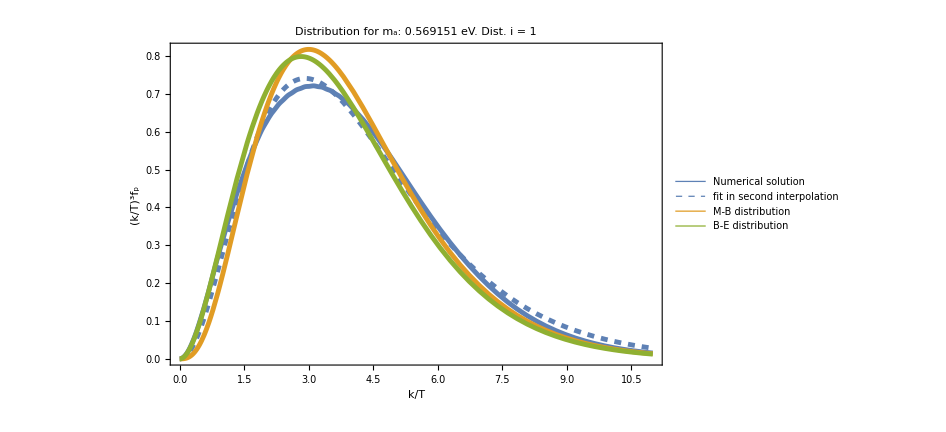

```mathematica
(********** Select distribution that we already have **********)
NumberOfDist=1;
SelectedDist=AxDistFunctionList[[NumberOfDist]];
SelectedMass=maValuesList[[NumberOfDist]];
SelectedFa = faValuesList[[NumberOfDist]];
Print["f_a: ", SelectedFa, " GeV"]
(********** Numerical Solution in second interpolation **********)
Avalue = polyModA[Log[SelectedMass]];
{{bvalue = polyModb[Log[SelectedMass]];}, {μvalue = polyModμ[Log[SelectedMass]];}}

(********** Define the distribution functions **********)
fBoltzmann[C_,x_]:=x^3 C Exp[- x]
fEinstein[C_,x_]:=x^3 C(Exp[x]-1)^(-1)

(********** Compute the integral of the selected distribution **********)
upperLimit=13;
integralF=NIntegrate[SelectedDist[x],{x,0,upperLimit}]

(********** Define the numerical integrals for the other functions **********)
integralFBoltzmann[C_]:=NIntegrate[fBoltzmann[C,x],{x,0,upperLimit}]
integralFEinstein[C_]:=NIntegrate[fEinstein[C,x],{x,0,upperLimit}]

(********** Solve for C using FindRoot **********)
solBoltzmann=FindRoot[integralF==integralFBoltzmann[C],{C,1}]
solEinstein=FindRoot[integralF==integralFEinstein[C],{C,1}]

(********** Display the solutions **********)
solBoltzmann
solEinstein

(********** Verify the solutions **********)
NIntegrate[fBoltzmann[C/. solBoltzmann,x],{x,0,upperLimit}]
NIntegrate[fEinstein[C/. solEinstein,x],{x,0,upperLimit}]

(********** Plot: Compare fit to Bose-Eintesin and Maxwell-Boltzmann distribution **********)
Plot[{SelectedDist[x], fApprox[x,Avalue,bvalue,μvalue], 
fBoltzmann[C/. solBoltzmann, x], 
fEinstein[C/. solEinstein, x]},{x,0,11},
Frame->True,FrameLabel->{{"(k/T)^3f_p",None},{"k/T",None}},LabelStyle->22,FrameStyle->Directive[Black,Thick],PlotStyle->{{Thickness[0.005],ColorData[97,1]},{Dashed,Thickness[0.005],ColorData[97,1]},
{Thickness[0.005],Orange,ColorData[97,2]},{Thickness[0.005],Green,ColorData[97,3]}},

PlotLegends->{"Numerical solution","fit in second interpolation", "M-B distribution", "B-E distribution"},
PlotLabel->"Distribution for m_a: "  <> ToString[SelectedMass] <> " eV. Dist. i = " <> ToString [NumberOfDist],
ImageSize-> 700]
```

## To presentation

f_a: 10000000 GeV

{{Null},{Null}}

3.64511

NIntegrate::inumr: The integrand C ⅇ^-x x^3 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,13}}.

{C→0.608157}

NIntegrate::inumr: The integrand (C x^3)/(-1+ⅇ^x) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,13}}.

{C→0.561855}

{C→0.608157}

{C→0.561855}

3.64511

3.64511

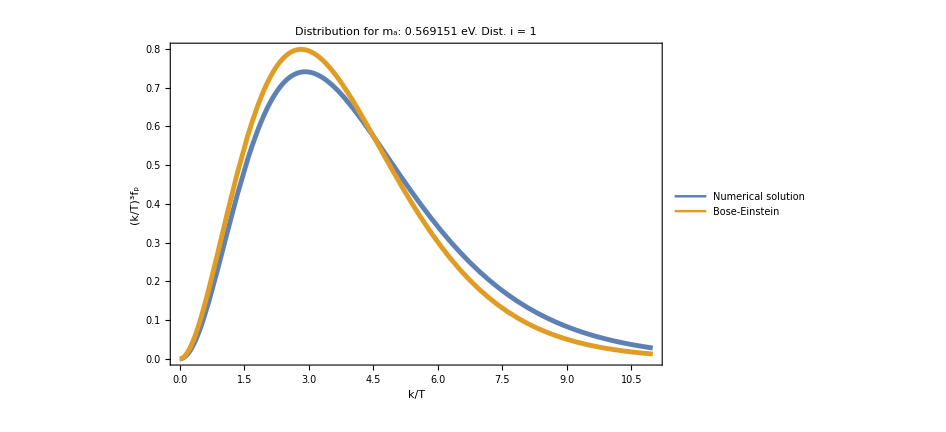

```mathematica
(********** Select distribution that we already have **********)
NumberOfDist=1;
SelectedDist=AxDistFunctionList[[NumberOfDist]];
SelectedMass=maValuesList[[NumberOfDist]];
SelectedFa = faValuesList[[NumberOfDist]];
Print["f_a: ", SelectedFa, " GeV"]
(********** Numerical Solution in second interpolation **********)
Avalue = polyModA[Log[SelectedMass]];
{{bvalue = polyModb[Log[SelectedMass]];}, {μvalue = polyModμ[Log[SelectedMass]];}}

(********** Define the distribution functions **********)
fBoltzmann[C_,x_]:=x^3 C Exp[- x]
fEinstein[C_,x_]:=x^3 C(Exp[x]-1)^(-1)

(********** Compute the integral of the selected distribution **********)
upperLimit=13;
integralF=NIntegrate[SelectedDist[x],{x,0,upperLimit}]

(********** Define the numerical integrals for the other functions **********)
integralFBoltzmann[C_]:=NIntegrate[fBoltzmann[C,x],{x,0,upperLimit}]
integralFEinstein[C_]:=NIntegrate[fEinstein[C,x],{x,0,upperLimit}]

(********** Solve for C using FindRoot **********)
solBoltzmann=FindRoot[integralF==integralFBoltzmann[C],{C,1}]
solEinstein=FindRoot[integralF==integralFEinstein[C],{C,1}]

(********** Display the solutions **********)
solBoltzmann
solEinstein

(********** Verify the solutions **********)
NIntegrate[fBoltzmann[C/. solBoltzmann,x],{x,0,upperLimit}]
NIntegrate[fEinstein[C/. solEinstein,x],{x,0,upperLimit}]

(********** Plot: Compare fit to Bose-Eintesin and Maxwell-Boltzmann distribution **********)
Plot[{fApprox[x,Avalue,bvalue,μvalue], 
fEinstein[C/. solEinstein, x]},{x,0,11},
Frame->True,FrameLabel->{{"(k/T)^3f_p",None},{"k/T",None}},LabelStyle->22,FrameStyle->Directive[Black,Thick],PlotStyle->{{Thickness[0.005],ColorData[97,1]},
{Thickness[0.005],Orange,ColorData[97,2]},{Thickness[0.005],Green,ColorData[97,3]}},

PlotLegends->{"Numerical solution", "Bose-Einstein"},
PlotLabel->"Distribution for m_a: "  <> ToString[SelectedMass] <> " eV. Dist. i = " <> ToString [NumberOfDist],
ImageSize-> 700]
```